```mathematica
Manipulate[
Module[{L,Ts1,k,h1,h2,Ts2,T2},
L=0.003;(*m or 3mm*)
Ts1=36;(*°C body temp*)
k=0.2;(*W/m/K conduction HT coeff of fatty tissue*)
h1=25;(*calm W/m2/K*)
h2=14.8*(v)^0.69;(*windy*)
Ts2[h_]=t/.Quiet@Solve[k*L^-1*(Ts1-t)==h*(t-Tsurr),t][[1]];
Graphics[{


}]
],
{{v,8,"wind speed (m/s)"},5,20,1,Appearance->"Labeled"},
{{Tsurr,-15,"air temperature (°C)"},-20,10,1,Appearance->"Labeled"}]
```

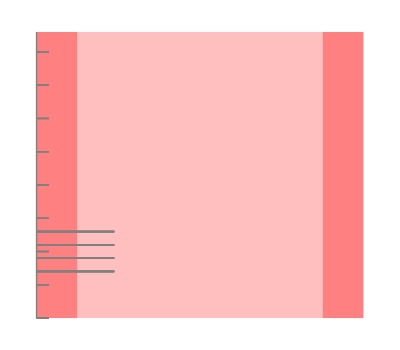

```mathematica
Graphics[{
{FaceForm[Pink],Rectangle[{-0.5,-5},{0,38}],Rectangle[{3,-5},{3.5,38}]},
{FaceForm[Opacity[0.5,Pink]],Rectangle[{0,-5},{3,38}]},
{Gray,Thin,Line[{{-0.5,-5},{-0.5,38}}]},
Table[{Gray,Thin,
Line[{{-0.5,i},{-0.35,i}}],
(*Line[{{-0.5,j},{-0.45,j}}]*)
Line[{{-0.5,j},{0.45,j}}]
},
{i,-5,35,5},
{j,2,8,2}]
},AspectRatio->Full,ImageSize->{400,350},PlotRangeClipping->False,ImagePadding->{{70,170},{Automatic,Automatic}}]
```

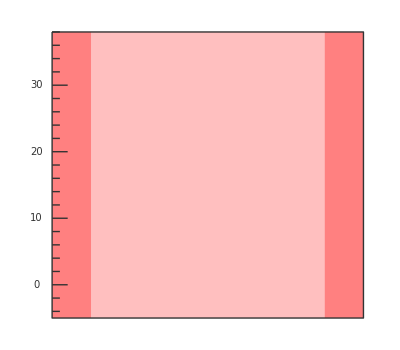

```mathematica
gray=GrayLevel[0.2];
Graphics[{
{FaceForm[Opacity[1,Pink]],Rectangle[{-0.5,-5},{0,38}],Rectangle[{3,-5},{3.5,38}]},
{FaceForm[Opacity[0.5,Pink]],Rectangle[{0,-5},{3,38}]},

{gray,Thin,Line[{{-0.5,38},{3.5,38},{3.5,-5},{-0.5,-5},{-0.5,38}}]},
Table[{
{gray,Line[{{-0.5,i},{-0.3,i}}]},
Text[Style[i,10,gray],{-0.7,i}]
},{i,0,30,10}],

Table[{Thin,gray,Line[{{-0.5,j},{-0.4,j}}]},{j,-4,-2,2}],
Table[{Thin,gray,
Line[{{-0.5,k},{-0.4,k}}],
Line[{{-0.5,10+k},{-0.4,10+k}}],
Line[{{-0.5,20+k},{-0.4,20+k}}],
Line[{{-0.5,30+k},{-0.4,30+k}}]
},{k,2,8,2}]

},AspectRatio->Full,ImageSize->{400,350},PlotRangeClipping->False,ImagePadding->{{70,170},{Automatic,Automatic}}]
```

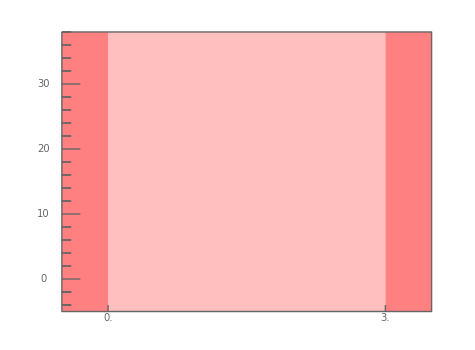

```mathematica
Module[{gray},
gray=GrayLevel[0.4];
Graphics[{
{FaceForm[Opacity[1,Pink]],Rectangle[{-2.5,-5},{0,38}],Rectangle[{15,-5},{15+2.5,38}]},
{FaceForm[Opacity[0.5,Pink]],Rectangle[{0,-5},{15,38}]},
{gray,Thin,Line[{{-2.5,38},{15+2.5,38},{15+2.5,-5},{-2.5,-5},{-2.5,38}}]},
Table[{{gray,Line[{{-2.5,i},{-1.5,i}}]},Text[Style[i,10,gray],{-3.5,i}]},{i,0,30,10}],
Table[{Thin,gray,
Line[{{-2.5,j},{-2,j}}],
Line[{{-2.5,k},{-2,k}}],
Line[{{-2.5,10+k},{-2,10+k}}],
Line[{{-2.5,20+k},{-2,20+k}}],
Line[{{-2.5,30+k},{-2,30+k}}]
},{j,-4,-2,2},{k,2,8,2}],
Table[{
{Thin,gray,Line[{{m,-5},{m,-4}}]},
Text[Style[0.2*m,10,gray],{m,-6}]
},{m,0,15,15}]

},ImageSize->{475,350}(*,PlotRange->{{-2,8},{-8,38}}*)]
]
```